```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/VV/west/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<cross-sectionNLOWest.res
```

```mathematica
mc=1.3;mb=4.;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=(22.6047)^2;mt=170;fBc=1;R1=R2=√((Pi m)/3) fBc;AL=1/137; nf=6;
```

```mathematica
R1
```

2.35588

```mathematica
(MC=1.3,MB=4,MT=170,alphaS=0.3,alpha=1/137,fBc=1,mu=2*(MC+MB))
```

```mathematica
Sqrt[4 m^2]
```

10.6

```mathematica
(2mc+2 mc)^2
```

27.04

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

-1.43101×10^-10 eps Aconj(1.3) AS^3-(6.2684×10^-13 Aconj(1.3) AS^3)/eps+1.42873×10^-10 Aconj(1.3) AS^3-5.58367×10^-12 eps Aconj(4.) AS^3+(2.03723×10^-13 Aconj(4.) AS^3)/eps+3.58956×10^-11 Aconj(4.) AS^3-7.09663×10^-13 eps Aconj(170.) AS^3+1.49712×10^-12 Aconj(170.) AS^3-3.82698×10^-10 eps Bconj(30.742,0.,0.) AS^3+4.28418×10^-10 Bconj(30.742,0.,0.) AS^3+1.25446×10^-11 eps Bconj(30.742,1.3,1.3) AS^3+(1.42743×10^-11 Bconj(30.742,1.3,1.3) AS^3)/eps-4.13471×10^-11 Bconj(30.742,1.3,1.3) AS^3-7.42844×10^-12 eps Bconj(30.742,4.,4.) AS^3-5.04033×10^-11 Bconj(30.742,4.,4.) AS^3-2.25821×10^-8 eps Bconj(30.742,170.,170.) AS^3-4.28433×10^-8 Bconj(30.742,170.,170.) AS^3+1.66962×10^-7 eps Bconj(101.881,1.3,4.) AS^3-(1.53744×10^-11 Bconj(101.881,1.3,4.) AS^3)/eps-1.23402×10^-7 Bconj(101.881,1.3,4.) AS^3-1.6694×10^-7 eps Bconj(101.881,4.,1.3) AS^3-(1.53744×10^-11 Bconj(101.881,4.,1.3) AS^3)/eps+1.2345×10^-7 Bconj(101.881,4.,1.3) AS^3-5.61225×10^-10 eps Bconj(141.333,0.,4.) AS^3+3.4912×10^-10 Bconj(141.333,0.,4.) AS^3+7.05373×10^-10 eps Bconj(141.333,4.,0.) AS^3-5.15982×10^-10 Bconj(141.333,4.,0.) AS^3-1.02638×10^-9 eps Bconj(291.049,0.,0.) AS^3+5.13239×10^-10 Bconj(291.049,0.,0.) AS^3-5.30903×10^-12 eps Bconj(291.049,1.3,1.3) AS^3-4.12007×10^-12 Bconj(291.049,1.3,1.3) AS^3-9.45564×10^-12 eps Bconj(291.049,4.,4.) AS^3+(1.42743×10^-11 Bconj(291.049,4.,4.) AS^3)/eps-1.80265×10^-11 Bconj(291.049,4.,4.) AS^3-1.63233×10^-10 eps Bconj(291.049,170.,170.) AS^3-4.48508×10^-10 Bconj(291.049,170.,170.) AS^3+2.0429×10^-9 eps Bconj(387.33,0.,1.3) AS^3-8.22122×10^-10 Bconj(387.33,0.,1.3) AS^3+1.07641×10^-10 eps Bconj(387.33,1.3,0.) AS^3-8.82429×10^-11 Bconj(387.33,1.3,0.) AS^3-1.10698×10^-9 eps Bconj(510.972,1.3,1.3) AS^3+3.90294×10^-10 Bconj(510.972,1.3,1.3) AS^3+2.84586×10^-10 eps Bconj(510.972,4.,4.) AS^3-3.3814×10^-10 Bconj(510.972,4.,4.) AS^3+8.47697×10^-10 eps Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3+8.17029×10^-10 Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3-5.07861×10^-9 eps Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3+5.8814×10^-9 Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3-8.3783×10^-11 eps Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+2.92326×10^-11 Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+1.52979×10^-9 eps Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3-3.97489×10^-9 Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3+1.91267×10^-10 eps Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-1.19673×10^-10 Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-4.52558×10^-8 eps Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+1.02833×10^-8 Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+2.67394×10^-8 eps Cconj(16.,30.742,141.333,0.,4.,0.) AS^3-1.47707×10^-8 Cconj(16.,30.742,141.333,0.,4.,0.) AS^3+3.45583×10^-10 eps Cconj(16.,141.333,30.742,4.,4.,0.) AS^3+3.73849×10^-11 Cconj(16.,141.333,30.742,4.,4.,0.) AS^3-2.45091×10^-8 eps Cconj(16.,141.333,510.972,4.,4.,0.) AS^3-1.45097×10^-8 Cconj(16.,141.333,510.972,4.,4.,0.) AS^3+5.99105×10^-10 eps Cconj(16.,291.049,16.,0.,4.,0.) AS^3-4.86922×10^-10 Cconj(16.,291.049,16.,0.,4.,0.) AS^3-2.83665×10^-9 eps Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+2.90122×10^-9 Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+3.59214×10^-11 eps Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-3.63256×10^-11 Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-8.31282×10^-11 eps Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3+3.51613×10^-10 Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3-8.3783×10^-11 eps Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3+2.92326×10^-11 Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3+3.45583×10^-10 eps Cconj(141.333,16.,30.742,4.,4.,0.) AS^3+3.73849×10^-11 Cconj(141.333,16.,30.742,4.,4.,0.) AS^3+9.05648×10^-8 eps Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-1.32899×10^-8 Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-5.31919×10^-9 eps Cconj(141.333,30.742,16.,0.,4.,0.) AS^3-1.06311×10^-8 Cconj(141.333,30.742,16.,0.,4.,0.) AS^3+1.91267×10^-10 eps Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3-1.19673×10^-10 Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3+3.59214×10^-11 eps Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3-3.63256×10^-11 Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3+3.53148×10^-8 eps Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-1.23348×10^-8 Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-1.06524×10^-9 eps Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3-7.95416×10^-10 Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3+6.04635×10^-10 log(0.245283) AS^3+9.0294×10^-10 log(0.754717) AS^3-7.53788×10^-10 log(0.0355999 mmu) AS^3-(1.27925×10^-9 AS^3)/eps-8.22665×10^-10 AS^3+4.71654×10^-10 AS^2+(-1.43101×10^-10 eps AS^3-(6.2684×10^-13 AS^3)/eps+1.42873×10^-10 AS^3) A(1.3)+(-5.58367×10^-12 eps AS^3+(2.03723×10^-13 AS^3)/eps+3.58956×10^-11 AS^3) A(4.)+(1.49712×10^-12 AS^3-7.09663×10^-13 AS^3 eps) A(170.)+(4.28418×10^-10 AS^3-3.82698×10^-10 AS^3 eps) B(30.742,0.,0.)+(1.25446×10^-11 eps AS^3+(1.42743×10^-11 AS^3)/eps-4.13471×10^-11 AS^3) B(30.742,1.3,1.3)+(-7.42844×10^-12 eps AS^3-5.04033×10^-11 AS^3) B(30.742,4.,4.)+(-2.25821×10^-8 eps AS^3-4.28433×10^-8 AS^3) B(30.742,170.,170.)+(1.66962×10^-7 eps AS^3-(1.53744×10^-11 AS^3)/eps-1.23402×10^-7 AS^3) B(101.881,1.3,4.)+(-1.6694×10^-7 eps AS^3-(1.53744×10^-11 AS^3)/eps+1.2345×10^-7 AS^3) B(101.881,4.,1.3)+(3.4912×10^-10 AS^3-5.61225×10^-10 AS^3 eps) B(141.333,0.,4.)+(7.05373×10^-10 AS^3 eps-5.15982×10^-10 AS^3) B(141.333,4.,0.)+(5.13239×10^-10 AS^3-1.02638×10^-9 AS^3 eps) B(291.049,0.,0.)+(-5.30903×10^-12 eps AS^3-4.12007×10^-12 AS^3) B(291.049,1.3,1.3)+(-9.45564×10^-12 eps AS^3+(1.42743×10^-11 AS^3)/eps-1.80265×10^-11 AS^3) B(291.049,4.,4.)+(-1.63233×10^-10 eps AS^3-4.48508×10^-10 AS^3) B(291.049,170.,170.)+(2.0429×10^-9 AS^3 eps-8.22122×10^-10 AS^3) B(387.33,0.,1.3)+(1.07641×10^-10 AS^3 eps-8.82429×10^-11 AS^3) B(387.33,1.3,0.)+(3.90294×10^-10 AS^3-1.10698×10^-9 AS^3 eps) B(510.972,1.3,1.3)+(2.84586×10^-10 AS^3 eps-3.3814×10^-10 AS^3) B(510.972,4.,4.)+(8.47697×10^-10 eps AS^3+8.17029×10^-10 AS^3) C[1.69,30.742,1.69,0,1.3,0]+(5.8814×10^-9 AS^3-5.07861×10^-9 AS^3 eps) C[1.69,141.333,28.09,4.,1.3,0]+(2.92326×10^-11 AS^3-8.3783×10^-11 AS^3 eps) C[1.69,141.333,101.881,4.,1.3,0]+(1.52979×10^-9 AS^3 eps-3.97489×10^-9 AS^3) C[1.69,291.049,387.33,0,1.3,0]+(1.91267×10^-10 AS^3 eps-1.19673×10^-10 AS^3) C[1.69,387.33,291.049,1.3,1.3,0]+(1.02833×10^-8 AS^3-4.52558×10^-8 AS^3 eps) C[1.69,387.33,510.972,1.3,1.3,0]+(2.67394×10^-8 AS^3 eps-1.47707×10^-8 AS^3) C[16.,30.742,141.333,0,4.,0]+(3.45583×10^-10 eps AS^3+3.73849×10^-11 AS^3) C[16.,141.333,30.742,4.,4.,0]+(-2.45091×10^-8 eps AS^3-1.45097×10^-8 AS^3) C[16.,141.333,510.972,4.,4.,0]+(5.99105×10^-10 AS^3 eps-4.86922×10^-10 AS^3) C[16.,291.049,16.,0,4.,0]+(2.90122×10^-9 AS^3-2.83665×10^-9 AS^3 eps) C[16.,387.33,28.09,1.3,4.,0]+(3.59214×10^-11 AS^3 eps-3.63256×10^-11 AS^3) C[16.,387.33,101.881,1.3,4.,0]+(3.51613×10^-10 AS^3-8.31282×10^-11 AS^3 eps) C[101.881,101.881,510.972,1.3,1.3,4.]+(2.92326×10^-11 AS^3-8.3783×10^-11 AS^3 eps) C[141.333,1.69,101.881,1.3,4.,0]+(3.45583×10^-10 eps AS^3+3.73849×10^-11 AS^3) C[141.333,16.,30.742,4.,4.,0]+(9.05648×10^-8 AS^3 eps-1.32899×10^-8 AS^3) C[141.333,16.,510.972,4.,4.,0]+(-5.31919×10^-9 eps AS^3-1.06311×10^-8 AS^3) C[141.333,30.742,16.,0,4.,0]+(1.91267×10^-10 AS^3 eps-1.19673×10^-10 AS^3) C[387.33,1.69,291.049,1.3,1.3,0]+(3.59214×10^-11 AS^3 eps-3.63256×10^-11 AS^3) C[387.33,16.,101.881,4.,1.3,0]+(3.53148×10^-8 AS^3 eps-1.23348×10^-8 AS^3) C[387.33,291.049,1.69,0,1.3,0]+(-1.06524×10^-9 eps AS^3-7.95416×10^-10 AS^3) C[510.972,101.881,101.881,1.3,4.,4.]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(4.23632+3.14159 ⅈ) eps log(mmu)+(6.03838+13.3088 ⅈ) eps-(4.23632+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-2.16138×10^-6+2.96229×10^-9 ⅈ) eps^2 AS^3-(2.17551×10^-8-8.08048×10^-23 ⅈ) eps^2 log^2(mmu) AS^3+(6.41825×10^-10-5.14692×10^-27 ⅈ) eps log^2(mmu) AS^3-(5.53541×10^-25-2.23593×10^-31 ⅈ) log^2(mmu) AS^3+(3.98436×10^-8-1.86116×10^-23 ⅈ) eps AS^3+(8.47697×10^-10-4.03897×10^-28 ⅈ) eps C[1.69,30.742,1.69,0,1.3,0] AS^3+(8.17029×10^-10-3.02923×10^-28 ⅈ) C[1.69,30.742,1.69,0,1.3,0] AS^3-(5.07861×10^-9-1.21169×10^-27 ⅈ) eps C[1.69,141.333,28.09,4.,1.3,0] AS^3+(5.8814×10^-9-1.21169×10^-27 ⅈ) C[1.69,141.333,28.09,4.,1.3,0] AS^3-(8.3783×10^-11-1.26218×10^-29 ⅈ) eps C[1.69,141.333,101.881,4.,1.3,0] AS^3+(2.92326×10^-11-6.31089×10^-30 ⅈ) C[1.69,141.333,101.881,4.,1.3,0] AS^3+(1.52979×10^-9-1.00974×10^-28 ⅈ) eps C[1.69,291.049,387.33,0,1.3,0] AS^3-(3.97489×10^-9-8.07794×10^-28 ⅈ) C[1.69,291.049,387.33,0,1.3,0] AS^3+(1.91267×10^-10-7.57306×10^-29 ⅈ) eps C[1.69,387.33,291.049,1.3,1.3,0] AS^3-(1.19673×10^-10-1.26218×10^-29 ⅈ) C[1.69,387.33,291.049,1.3,1.3,0] AS^3-(4.52558×10^-8-9.69352×10^-27 ⅈ) eps C[1.69,387.33,510.972,1.3,1.3,0] AS^3+(1.02833×10^-8-2.42338×10^-27 ⅈ) C[1.69,387.33,510.972,1.3,1.3,0] AS^3+2.67394×10^-8 eps C[16.,30.742,141.333,0,4.,0] AS^3-(1.47707×10^-8+1.43493×10^-42 ⅈ) C[16.,30.742,141.333,0,4.,0] AS^3+(3.45583×10^-10-5.04871×10^-29 ⅈ) eps C[16.,141.333,30.742,4.,4.,0] AS^3+3.73849×10^-11 C[16.,141.333,30.742,4.,4.,0] AS^3-2.45091×10^-8 eps C[16.,141.333,510.972,4.,4.,0] AS^3-(1.45097×10^-8-4.84676×10^-27 ⅈ) C[16.,141.333,510.972,4.,4.,0] AS^3+(5.99105×10^-10-1.00974×10^-28 ⅈ) eps C[16.,291.049,16.,0,4.,0] AS^3-4.86922×10^-10 C[16.,291.049,16.,0,4.,0] AS^3-(2.83665×10^-9-8.07794×10^-28 ⅈ) eps C[16.,387.33,28.09,1.3,4.,0] AS^3+(2.90122×10^-9-2.01948×10^-28 ⅈ) C[16.,387.33,28.09,1.3,4.,0] AS^3+(3.59214×10^-11-1.4013×10^-45 ⅈ) eps C[16.,387.33,101.881,1.3,4.,0] AS^3-(3.63256×10^-11-9.46633×10^-30 ⅈ) C[16.,387.33,101.881,1.3,4.,0] AS^3-(8.31282×10^-11-1.89327×10^-29 ⅈ) eps C[101.881,101.881,510.972,1.3,1.3,4.] AS^3+(3.51613×10^-10-7.57306×10^-29 ⅈ) C[101.881,101.881,510.972,1.3,1.3,4.] AS^3-(8.3783×10^-11-1.26218×10^-29 ⅈ) eps C[141.333,1.69,101.881,1.3,4.,0] AS^3+(2.92326×10^-11-6.31089×10^-30 ⅈ) C[141.333,1.69,101.881,1.3,4.,0] AS^3+(3.45583×10^-10-5.04871×10^-29 ⅈ) eps C[141.333,16.,30.742,4.,4.,0] AS^3+3.73849×10^-11 C[141.333,16.,30.742,4.,4.,0] AS^3+(9.05648×10^-8-1.9387×10^-26 ⅈ) eps C[141.333,16.,510.972,4.,4.,0] AS^3-(1.32899×10^-8+1.43493×10^-42 ⅈ) C[141.333,16.,510.972,4.,4.,0] AS^3-(5.31919×10^-9-4.03897×10^-28 ⅈ) eps C[141.333,30.742,16.,0,4.,0] AS^3-(1.06311×10^-8-1.61559×10^-27 ⅈ) C[141.333,30.742,16.,0,4.,0] AS^3+(1.91267×10^-10-7.57306×10^-29 ⅈ) eps C[387.33,1.69,291.049,1.3,1.3,0] AS^3-(1.19673×10^-10-1.26218×10^-29 ⅈ) C[387.33,1.69,291.049,1.3,1.3,0] AS^3+(3.59214×10^-11-1.4013×10^-45 ⅈ) eps C[387.33,16.,101.881,4.,1.3,0] AS^3-(3.63256×10^-11-9.46633×10^-30 ⅈ) C[387.33,16.,101.881,4.,1.3,0] AS^3+(3.53148×10^-8-3.23117×10^-27 ⅈ) eps C[387.33,291.049,1.69,0,1.3,0] AS^3-(1.23348×10^-8+8.07794×10^-28 ⅈ) C[387.33,291.049,1.69,0,1.3,0] AS^3-(1.06524×10^-9-2.01948×10^-28 ⅈ) eps C[510.972,101.881,101.881,1.3,4.,4.] AS^3-(7.95416×10^-10-1.51461×10^-28 ⅈ) C[510.972,101.881,101.881,1.3,4.,4.] AS^3+(8.47697×10^-10-4.03897×10^-28 ⅈ) eps Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3+(8.17029×10^-10-3.02923×10^-28 ⅈ) Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3-(5.07861×10^-9-1.21169×10^-27 ⅈ) eps Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3+(5.8814×10^-9-1.21169×10^-27 ⅈ) Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3-(8.3783×10^-11-1.26218×10^-29 ⅈ) eps Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+(2.92326×10^-11-6.31089×10^-30 ⅈ) Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+(1.52979×10^-9-1.00974×10^-28 ⅈ) eps Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3-(3.97489×10^-9-8.07794×10^-28 ⅈ) Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3+(1.91267×10^-10-7.57306×10^-29 ⅈ) eps Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-(1.19673×10^-10-1.26218×10^-29 ⅈ) Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-(4.52558×10^-8-9.69352×10^-27 ⅈ) eps Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+(1.02833×10^-8-2.42338×10^-27 ⅈ) Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+2.67394×10^-8 eps Cconj(16.,30.742,141.333,0.,4.,0.) AS^3-(1.47707×10^-8+1.43493×10^-42 ⅈ) Cconj(16.,30.742,141.333,0.,4.,0.) AS^3+(3.45583×10^-10-5.04871×10^-29 ⅈ) eps Cconj(16.,141.333,30.742,4.,4.,0.) AS^3+3.73849×10^-11 Cconj(16.,141.333,30.742,4.,4.,0.) AS^3-2.45091×10^-8 eps Cconj(16.,141.333,510.972,4.,4.,0.) AS^3-(1.45097×10^-8-4.84676×10^-27 ⅈ) Cconj(16.,141.333,510.972,4.,4.,0.) AS^3+(5.99105×10^-10-1.00974×10^-28 ⅈ) eps Cconj(16.,291.049,16.,0.,4.,0.) AS^3-4.86922×10^-10 Cconj(16.,291.049,16.,0.,4.,0.) AS^3-(2.83665×10^-9-8.07794×10^-28 ⅈ) eps Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+(2.90122×10^-9-2.01948×10^-28 ⅈ) Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+(3.59214×10^-11-1.4013×10^-45 ⅈ) eps Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-(3.63256×10^-11-9.46633×10^-30 ⅈ) Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-(8.31282×10^-11-1.89327×10^-29 ⅈ) eps Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3+(3.51613×10^-10-7.57306×10^-29 ⅈ) Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3-(8.3783×10^-11-1.26218×10^-29 ⅈ) eps Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3+(2.92326×10^-11-6.31089×10^-30 ⅈ) Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3+(3.45583×10^-10-5.04871×10^-29 ⅈ) eps Cconj(141.333,16.,30.742,4.,4.,0.) AS^3+3.73849×10^-11 Cconj(141.333,16.,30.742,4.,4.,0.) AS^3+(9.05648×10^-8-1.9387×10^-26 ⅈ) eps Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-(1.32899×10^-8+1.43493×10^-42 ⅈ) Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-(5.31919×10^-9-4.03897×10^-28 ⅈ) eps Cconj(141.333,30.742,16.,0.,4.,0.) AS^3-(1.06311×10^-8-1.61559×10^-27 ⅈ) Cconj(141.333,30.742,16.,0.,4.,0.) AS^3+(1.91267×10^-10-7.57306×10^-29 ⅈ) eps Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3-(1.19673×10^-10-1.26218×10^-29 ⅈ) Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3+(3.59214×10^-11-1.4013×10^-45 ⅈ) eps Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3-(3.63256×10^-11-9.46633×10^-30 ⅈ) Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3+(3.53148×10^-8-3.23117×10^-27 ⅈ) eps Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-(1.23348×10^-8+8.07794×10^-28 ⅈ) Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-(1.06524×10^-9-2.01948×10^-28 ⅈ) eps Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3-(7.95416×10^-10-1.51461×10^-28 ⅈ) Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3+(4.22836×10^-7-1.31839×10^-10 ⅈ) eps^2 log(mmu) AS^3+(8.99643×10^-10-2.35746×10^-23 ⅈ) eps log(mmu) AS^3-((1.10506×10^-24-3.58732×10^-43 ⅈ) log(mmu) AS^3)/eps+(5.25463×10^-10+6.551×10^-27 ⅈ) log(mmu) AS^3-((5.32777×10^-21-7.27014×10^-27 ⅈ) AS^3)/eps-((1.10864×10^-24+1.80351×10^-30 ⅈ) AS^3)/eps^2+(1.52866×10^-9+4.63997×10^-24 ⅈ) AS^3+(4.71654×10^-10-1.00974×10^-28 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

5.25463×10^-10 AS^3 log(mmu)-1.57049×10^-9 AS^3+4.71654×10^-10 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-18)],AS]/.{AS-> z *0.3}//Expand
```

1.41875×10^-11 z^3 log(mmu)-4.24034×10^-11 z^3+4.24489×10^-11 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

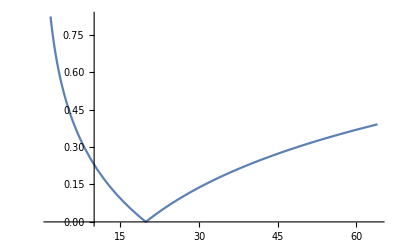

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.360215

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

0.115853

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 m)^2}],10^(-9)]
```

9.57374 z^3+16.5296 z^2

```mathematica
(* 
sqrt(s)=15.1047 GeV sigma(VV)=203.64 fb+142.77 fb
sqrt(s)=22.6047 GeV sigma(VV)=16.300 fb+9.3518 fb
sqrt(s)=27.6047 GeV sigma(VV)=4.0969 fb+1.9463 fb
*)
```